```mathematica
SetDirectory["G:\\My Drive\\Projects\\FourierDisplay\\Software"];
LoadPack:=Get["G:\\My Drive\\Projects\\FourierDisplay\\Software\\FourierPack.wl"];

LoadPack;
```

```mathematica
testImage = ColorNegate@Binarize@Import["G:\\My Drive\\Projects\\FourierDisplay\\Software\\Resources\\HandwritingImages\\JohnHancock.png"]
```

-Graphics-

```mathematica
Head@testImage
```

Image

```mathematica
processedImage = DeleteBorderComponents@Thinning@testImage
```

-Graphics-

```mathematica
points = N@PixelValuePositions[processedImage,White];
Length@points
```

1715

```mathematica
pointsTour = Last@FindShortestTour@points;
```

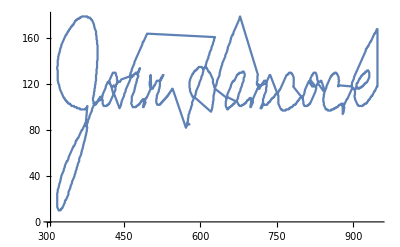

```mathematica
ListLinePlot@points[[pointsTour]]
```

## Test Function

```mathematica
image = Import["G:\\My Drive\\Projects\\FourierDisplay\\Software\\Resources\\HandwritingImages\\JohnHancock.png"];
```

```mathematica
ImageLinePoints[image_Image]:=Module[{processedImage, points},
processedImage = DeleteBorderComponents@Thinning@ColorNegate@Binarize@image;
points = N@PixelValuePositions[processedImage, White];
Return[points]];
```

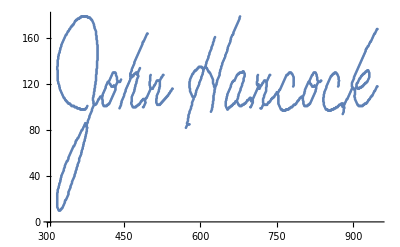

```mathematica
ListPlot@ImageLinePoints@image
```

```mathematica
Remove[ImageLinePoints];
```

```mathematica
points = ImageLinePoints@image;
```

```mathematica
pointsTour = MakeTour[points];
```

```mathematica
ListLinePlot[pointsTour]
```

-Graphics-

## Other Images

```mathematica
baseDir = "G:\\My Drive\\Projects\\FourierDisplay\\Software\\Resources\\HandwritingImages\\";
imageDirs = baseDir<>#&/@{"Renkert.jpg", "Phil.jpg"};
images = Import/@imageDirs;
```

```mathematica
processedImages = (ImageResize[ImageRotate@ImageAdjust[#,{1,.5}],1000])&/@images
```

{-Graphics-,-Graphics-}

```mathematica
points = ImageLinePoints/@processedImages;
```

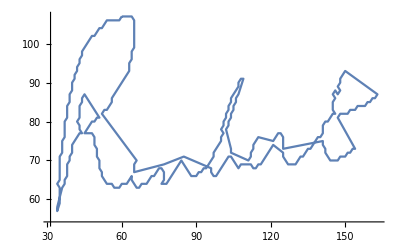
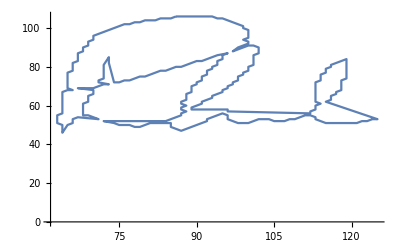

```mathematica
ListLinePlot@*MakeTour/@points
```

## Tweaking the FindShortestTour Algorithm

```mathematica
Options[MakeTour]={"StartFunction"->None};
MakeTour[data_, opts:OptionsPattern[{FindShortestTour,MakeTour}]]:=Module[{startFunc = OptionValue["StartFunction"],sortedDat, tour, points},
	sortedDat = If[startFunc===None,data,SortBy[data,startFunc]];
tour = Last@FindShortestTour[data, FilterRules[{opts},Options[{FindShortestTour}]]];
	points = sortedDat[[tour]];
	Return[points]];
```

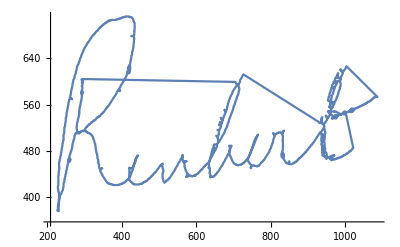
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot@MakeTour[points[[1]], Method->#, PerformanceGoal->"Quality"]&/@{"AllTours","CCA","Greedy","GreedyCycle","IntegerLinearProgramming","OrOpt","OrZweig","RemoveCrossings","SpaceFillingCurve","SimulatedAnnealing","TwoOpt", "Dijkstra", "Test"}
```

```mathematica
Options[FindShortestTour]
```

{DirectedEdges→False,DistanceFunction→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,WorkingPrecision→MachinePrecision}